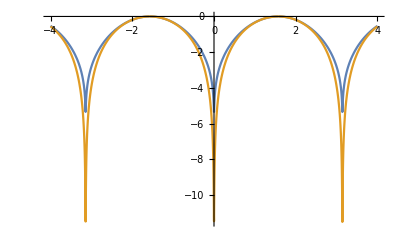

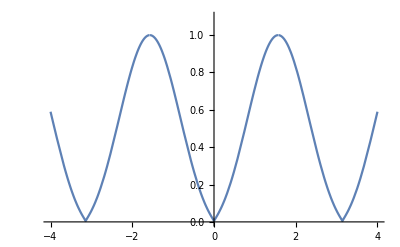

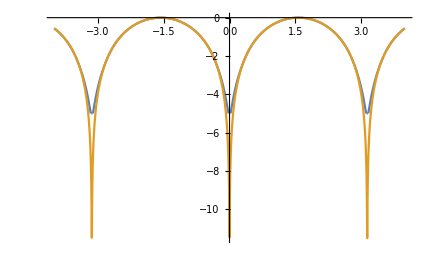

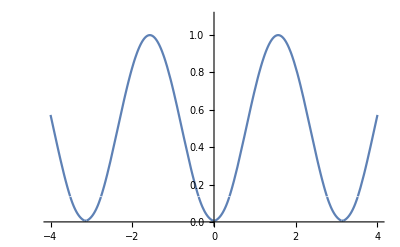

```mathematica
AsymptoticThreshold[x_,threshold_]:=If[x>0,x,x/(1+x/threshold)]
PolynomialThreshold[x_,thresh_,width_]:=If[x<thresh-width,thresh,If[x>thresh+width,x,(- thresh x+(thresh+width+x)^2/4)/width]]

threshold = -10;
plotWidth = 4;
avoidZero = 10^(-100/20);
Plot[{AsymptoticThreshold[Log[Sin[x]^2+avoidZero],threshold],Log[Sin[x]^2+avoidZero]},{x,-plotWidth,plotWidth},PlotRange->All]

Plot[ⅇ^AsymptoticThreshold[Log[Sin[x]^2+avoidZero],threshold],{x,-plotWidth,plotWidth},PlotRange->{All,{0,1.1}}]

Plot[{PolynomialThreshold[Log[Sin[x]^2+avoidZero],-5,3],Log[Sin[x]^2+avoidZero]},{x,-plotWidth,plotWidth},PlotRange->All]

Plot[ⅇ^PolynomialThreshold[Log[Sin[x]^2+avoidZero],-5,3],{x,-plotWidth,plotWidth},PlotRange->{All,{0,1.1}}]
```

```mathematica
(* f[0]== 0, f'[0]== 1, f'[threshold] == 0, f[threshold]==? *)
f[x_,a_,b_,c_]:=a x^2 + b x + c 
df[x_,a_,b_]:=2 a x + b 
soln = Solve[{f[u,a,b,c]== u,df[u,a,b]==1,df[l,a,b]==0},{a,b,c}];
f[x,a,b,c]/.soln//FullSimplify
```

{-(u^2-2 l x+x^2)/(2 l-2 u)}

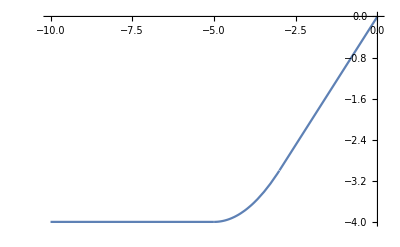

```mathematica
f[x_,l_,u_]:=-(u^2-2 l x+x^2)/(2 l-2 u)
ft[x_,tl_,tu_]:= If[x<tl,(tl+tu)/2,If[x>tu,x,f[x,tl,tu]]]
ftc[x_,l_,u_]:=ft[x,u-2(u-l),u];
Plot[ftc[x,-4,-3],{x,-10,0}]
```

```mathematica
ftc[x,l,u]//FullSimplify
f[x,u-2 (-l+u),u]//FullSimplify
```

If[u+x<2 l,1/2 ((u-2 (-l+u))+u),If[x>u,x,f[x,u-2 (-l+u),u]]]

-(-4 l x+(u+x)^2)/(4 (l-u))

```mathematica
f[x,u-2 (-l+u),u]//FullSimplify
```

-(-4 l x+(u+x)^2)/(4 (l-u))

```mathematica
FFinal[x_,l_,w_]:=If[x<l-w,l,If[x>l+w,x,(- l x+(l+w+x)^2/4)/w]]
Plot[FFinal[x,-4,1],{x,-10,0}]
```

-Graphics-